```mathematica
EulerAnglesToMatrix[pyr_] := Module[{
CP = Cos[pyr[[1]]], 
SP = Sin[pyr[[1]]],
CY = Cos[pyr[[2]]],
SY = Sin[pyr[[2]]],
CR = Cos[pyr[[3]]],
SR = Sin[pyr[[3]]]
},
({{CP CY, CY SP SR-CR SY, -CR CY SP-SR SY}, {CP SY, CR CY+SP SR SY, CY SR-CR SP SY}, {SP, -CP SR, CP CR}})
]
```

```mathematica
ImportEpisode[filename_] := Module[{data, n , car, inputs},
data = Import[filename, "CSV"];
n = Length[data];
car = {};
inputs = {};
Do[
AppendTo[car, <|
"pos"-> data[[i,1;;3]],
"vel"-> data[[i,4;;6]],
"θ"-> EulerAnglesToMatrix[data[[i, 7;;9]] * π/32768.0],
"ω"-> data[[i,10;;12]],
"sup"-> data[[i,13]],
"jump"-> data[[i,14]],
"dblj"-> data[[i,15]],
"grnd"-> data[[i,16]],
"boost"-> data[[i,17]],
"time"->0.0
|>];
AppendTo[inputs, <|
"thr"-> data[[i,18]],
"steer"-> data[[i,19]],
"pitch"-> data[[i,20]],
"yaw"-> data[[i,21]],
"roll"-> data[[i,22]],
"jump"-> data[[i,23]],
"boost"-> data[[i,24]],
"brake"-> data[[i,25]]
|>];
,
{i, 1, n}
];
{car, inputs}
]
```

```mathematica
drawPlots[] := {which = "pos";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car], PlotRange->All],
ImageSize->Large
],

which = "vel";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car], PlotRange->All],
ImageSize->Large
],

which = "ω";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car], PlotRange->All],
PlotRange->All,
ImageSize->Large
]}
```

```mathematica
1350 κ[1350]
```

2.2545

InterpolatingFunction[…]

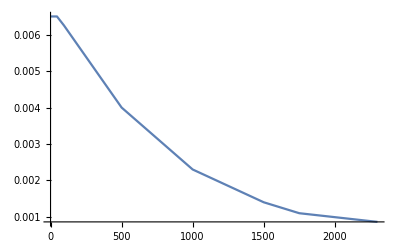

```mathematica
κ = Interpolation[({{0, 0.0065}, {50, 0.0065}, {500, 0.004}, {1000, 0.0023}, {1500, 0.0014}, {1750, 0.0011}, {2500, 0.000775}}), InterpolationOrder->1]
Plot[κ[x], {x, 0, 2300}]
```

```mathematica
g = -650.0;
boostAccel = 1000.0;
timeLimit = 0.3;
ωMaxAerial= 5.5;
drivingSpeed = 1450;
brakingForce = 3500;
coastingForce = 525;
throttleThreshold = 0.05;
throttleForce = 1550;
maxSpeed = 2275;
minSpeed = 10;

ωMax[speed_] := Module[{breaks = {0, 500, 1000, 1500, 1750, 2500}},
Piecewise[{{InterpolatingPolynomial[{{breaks[[1]], a0}, {1/2(breaks[[1]]+breaks[[2]]), a1}, {breaks[[2]], a2}}, speed], breaks[[1]] ≤ speed < breaks[[2]]}, {InterpolatingPolynomial[{{breaks[[2]], a2}, {1/2(breaks[[2]]+breaks[[3]]), a3}, {breaks[[3]], a4}}, speed], breaks[[2]] ≤ speed < breaks[[3]]}, {InterpolatingPolynomial[{{breaks[[3]], a4}, {1/2(breaks[[3]]+breaks[[4]]), a5}, {breaks[[4]], a6}}, speed], breaks[[3]] ≤ speed < breaks[[4]]}, {InterpolatingPolynomial[{{breaks[[4]], a6}, {1/2(breaks[[4]]+breaks[[5]]), a7}, {breaks[[5]], a8}}, speed], breaks[[4]] ≤ speed < breaks[[5]]}, {InterpolatingPolynomial[{{breaks[[5]], a8}, {1/2(breaks[[5]]+breaks[[6]]), a9}, {breaks[[6]], a10}}, speed], breaks[[5]] ≤ speed < breaks[[6]]}}]
] /. 
{a0->0.0361197319396348,a1->1.4230071171910135,a2->2.000625353083435,a3->2.381968265166805,a4->2.325659698093981,a5->2.33255995946433,a6->2.0282313684525564,a7->2.018237842179648,a8->1.9605648826662732,a9->2.006757348932908,a10->1.941542947128422}

κ = Interpolation[({{0, 0.00675 1.5}, {500, 0.004}, {1000, 0.0023}, {1500, 0.0014}, {1750, 0.0011}, {2500, 0.000775}}), InterpolationOrder->1]

AirDodge[state_, input_, Δt_] := Module[{
next = state

},
(* TODO *)
next
]

AerialControl[state_, input_, Δt_] := Module[{
next = state,
AirTorque = {-36.07956616966136, -12.145997819080709, 8.919628042877859},
AirDamping  = {-4.471663022015913, -2.798194258050845, -1.8864919004372327},
θ = state["θ"],
rpy = {input["roll"], input["pitch"], input["yaw"]},
ωAvg, ωLocal, T, Dd, α
},
next["vel"]=state["vel"] + ({0, 0, g}  + input["boost"] θ[[All, 1]]boostAccel)Δt;
next["pos"]=state["pos"] + next["vel"] Δt; 
T = DiagonalMatrix[AirTorque];
Dd = DiagonalMatrix[{
AirDamping[[1]], 
AirDamping[[2]](1-Abs[rpy[[2]]]), 
AirDamping[[3]](1-Abs[rpy[[3]]])
}];
next["ω"] = state["ω"] + θ.(T.rpy+ Dd.Transpose[θ].state["ω"]) Δt ;
next["ω"] *= Min[1.0, ωMaxAerial/Norm[next["ω"]]];
ωAvg = 1/2(state["ω"] + next["ω"]);
next["θ"] = RotationMatrix[Norm[ωAvg]Δt,Normalize[ωAvg]].θ;
next
]

drivingForceForward[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"],
turnDamping
},
turnDamping = (-0.07186693033945346 Abs[steering]-0.055453237281917644  Abs[ωu]+0.0006255296371672214 Abs[vl]) vf;
If[boost == 1,

(* boosting *)
If[vf < 0,
brakingForce,
If[0 <vf <drivingSpeed,
(maxSpeed - Abs[vf]),
If[vf > maxSpeed,
98.25785130764065 Abs[ωu],
boostAccel +turnDamping
]
]
],

(* not boosting *)
If[throttle * vf > -35, 
If[Abs[throttle] <  throttleThreshold && Abs[vf] > minSpeed,
-coastingForce Sign[vf] + turnDamping,
If[Abs[vf]>drivingSpeed,
turnDamping,
throttle(throttleForce - Abs[vf]) + turnDamping
]
],
brakingForce Sign[throttle]
]
]
]
{a->-7.82811881088291,b->15.006402973550104,c->-1380.4531378064655,d->-668.1208332047357,e->2.6698340502063305}
drivingForceLeft[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"],
turnDamping
},
 (1380.4531378064655 steering+7.82811881088291 throttle-15.006402973550104 vl+668.1208332047357 ωu)(1-Exp[-0.0011607974131331873 Abs[vf]])
]




GroundControl[state_, input_, Δt_] := Module[{
next = state,
forward=(state["θ"][[All, 1]]),
left=(state["θ"][[All, 2]]),
up=(state["θ"][[All, 3]]),
Fforward,Fleft,Tup
},
Fforward=drivingForceForward[state, input];
Fleft=drivingForceLeft[state, input];
Tup=drivingTorqueUp[state, input];
next["vel"]=state["vel"] + (Fforward*forward + Fleft*left) Δt;
next["pos"]=state["pos"] + next["vel"]Δt;
next["ω"]= state["ω"] + Tup*up Δt;
next["θ"]=RotationMatrix[next["ω"].up Δt, up].state["θ"];
next
]

GroundControlHandbrake[state_, input_, Δt_] := Module[{next = state},
(* TODO *)
next
]

Jump[state_, input_, Δt_] := Module[{
next = state,
θ = state["θ"]
},
next["grnd"] = 0;
next["jump"]= 1;
next["time"]= Δt;
(* TODO *)
next
]

CarControl[state_, input_, Δt_] := 
If[state["grnd"] == 1,
If[input["jump"] == 1,
Jump[state, input, Δt],
If[input["brake"] == 1,
GroundControlHandbrake[state, input, Δt],
GroundControl[state, input, Δt]
]
],
If[(input["jump"]==1)&&(state["time"]<timeLimit)&&(state["dblj"]==0),
AirDodge[state, input, Δt],
AerialControl[state, input, Δt]
]
]
```

InterpolatingFunction[…]

{a→-7.82812,b→15.0064,c→-1380.45,d→-668.121,e→2.66983}

```mathematica
Δt = 0.016366612111292964;
episode=6;
directory = "ground_driving_no_handbrake";
suffix = directory <> "/episode_" <>StringPadLeft[ToString[episode], 2, "0"] <> ".csv";
filename = NotebookDirectory[] <> suffix;

{car, inputs} = ImportEpisode[filename];
```

```mathematica
filename
```

C:\Users\sam\Documents\GitHub\Lobot\doc\car_control\ground_driving_no_handbrake/episode_06.csv

```mathematica
NotebookDirectory[] <> directory <> "/driving.txt"
```

C:\Users\sam\Documents\GitHub\Lobot\doc\car_control\ground_driving_no_handbrake/driving.txt

```mathematica
{car, inputs} = ImportEpisode[NotebookDirectory[] <> directory <> "/driving.txt"];
```

```mathematica
Length[car]
```

16352

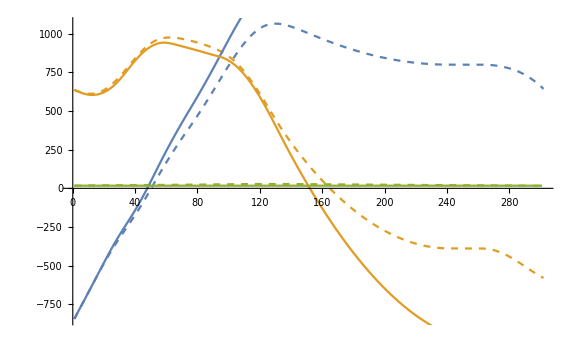
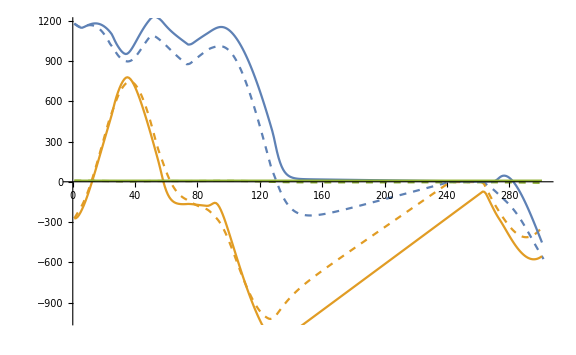
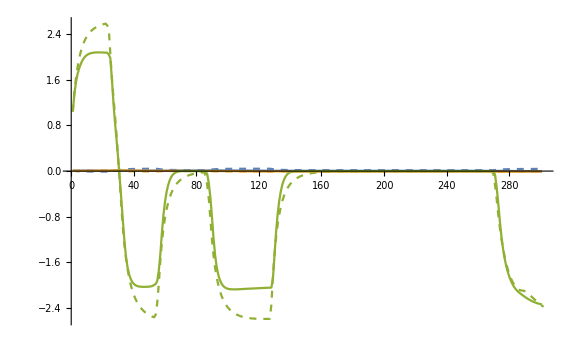

```mathematica
delay = 1;
predictions = {car[[1]]};
Do[
AppendTo[predictions, CarControl[predictions[[-1]], inputs[[i]], Δt]]
,
{i, 1, Length[car]}
]
drawPlots[]
```

```mathematica
ListLinePlot[#["steer"]& /@ inputs]
```

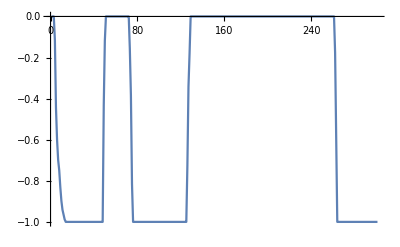

```mathematica
ListLinePlot[#["thr"]& /@ inputs]
```

```mathematica
range = 5000;;9000
```

5000;;9000

```mathematica
q[v_] := If[v < 0, -0.75, 1.0];
```

```mathematica
ω = {car[[range[[1]]]]["ω"]};
Do[
steering=inputs[[i-1]]["steer"];
vNorm = Norm[car[[i]]["vel"]];
vf=(car[[i]]["θ"][[All, 1]]).car[[i]]["vel"];
ωu=(car[[i]]["θ"][[All, 3]]).ω[[-1]];
τ = 16(Sign[vf] steering κ[Abs[vf]]vNorm - ωu);
AppendTo[ω, ω[[-1]] + {0, 0,τ} Δt]
,
{i,range[[1]]+1, range[[2]]}
]
```

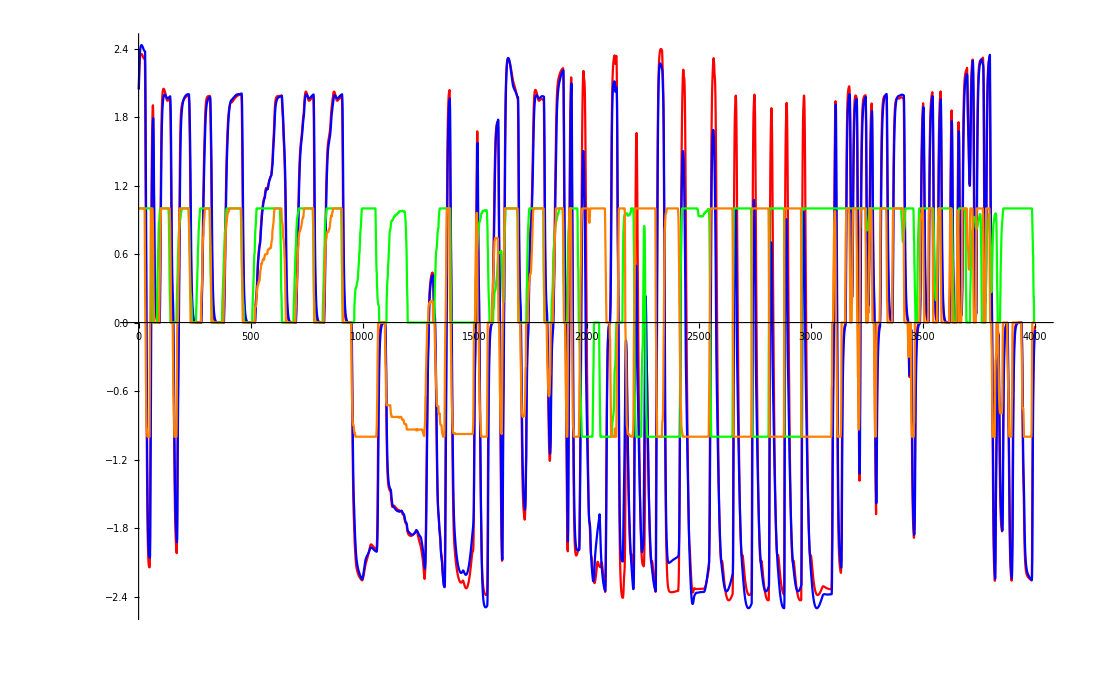

```mathematica
ListLinePlot[{
ω[[All, 3]], 
#["ω"][[3]]& /@ car[[range]], 
#["thr"]& /@ inputs[[range]],
#["steer"]& /@ inputs[[range]]
}, PlotRange->All, PlotStyle->{Red, Blue, Green, Orange}]
```

```mathematica
inputs[[100]]
```

<|thr→-1.,steer→0.999969,pitch→0.24408,yaw→0.999969,roll→0.,jump→0,boost→0,brake→0|>

```mathematica
car[[100]]
```

<|pos→{961.034,825.528,17.01},vel→{1132.69,-372.109,8.36},θ→{{-0.895069,-0.445846,-0.00858296},{0.445817,-0.895109,0.00513188},{-0.00997071,0.000766952,0.99995}},ω→{0.010202,0.,-2.06341},sup→0,jump→0,dblj→0,grnd→1,boost→100,time→0.|>

```mathematica
which = "ω";
delta = ((#[which]& /@ car[[2;;-1]])-(#[which]& /@ car[[1;;-2]]))/Δt
```

{{0.,-0.0290225,23.2756},{0.,-0.0000611,20.4038},{0.,-0.0245011,28.3621},{0.,-0.03055,34.7432},{0.,0.0170469,27.6783},{0.,0.0353769,21.1699},289,{-0.0226681,0.0083096,3.01125},{-0.0707538,0.0241956,9.95117},{-0.0506519,0.0102648,13.0827},{-0.0546234,0.01222,16.6314},{-0.0606723,0.0135642,21.0119}}
 |  |  |  |

```mathematica
drivingTorqueUp[state_, input_] := Module[{
steering=input["steer"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"]
},
15(Sign[vf] steering κ[Norm[state["vel"]]] Norm[state["vel"]] - ωu + 0.001vl)
]
```

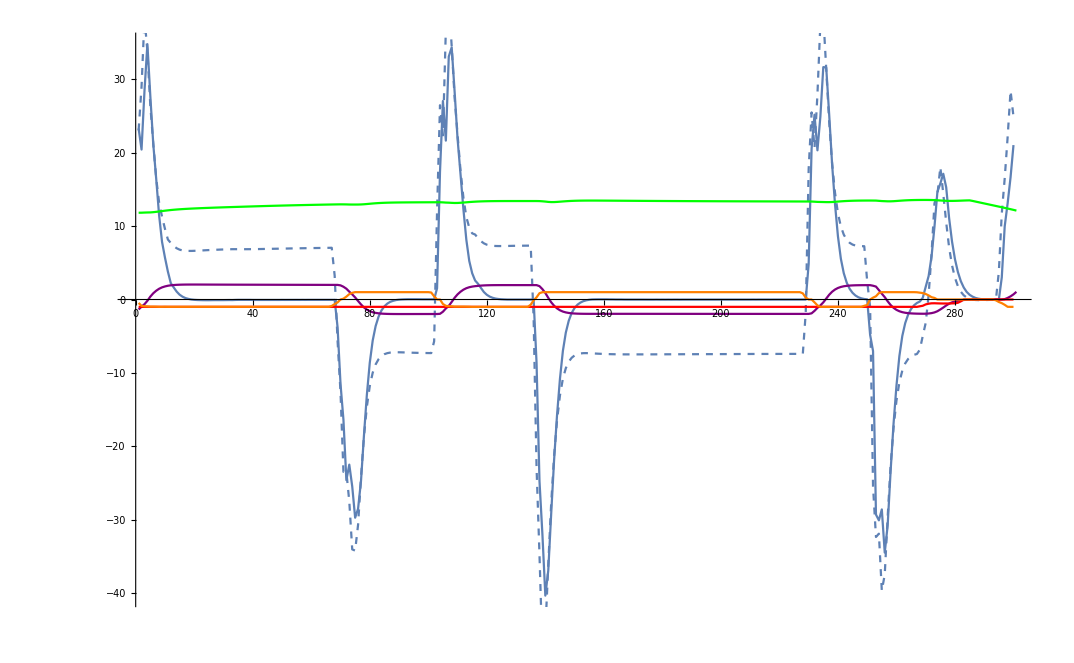

```mathematica
τ = Table[drivingTorqueUp[car[[i]], inputs[[i]]], {i, 1, Length[inputs]-1}];
Show[
ListLinePlot[delta[[All, 3]], PlotRange->All],
ListLinePlot[τ, PlotRange->All, PlotStyle->Dashed],
ListLinePlot[0.01Norm[#["vel"]]& /@ car, PlotRange->All, PlotStyle->Green],
ListLinePlot[#["ω"][[3]]& /@ car, PlotRange->All, PlotStyle->Purple],
ListLinePlot[#["thr"]& /@ inputs[[2;;-1]], PlotRange->All, PlotStyle->Red],
ListLinePlot[#["steer"]& /@ inputs[[2;;-1]], PlotRange->All, PlotStyle->Orange]
]
```

```mathematica
#["steer"]& /@ inputs[[2;;-1]]
```

{-0.464539,-0.866089,-0.921204,-0.936951,-0.968445,-0.968445,-0.976318,-0.992065,-0.992065,-0.984192,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,-0.992065,234,0.929077,0.873962,0.747986,0.559021,0.314941,0.212585,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.110229,-0.338562,-0.496033,-0.724365,-0.992065,-0.999969,-0.999969}
 |  |  |  |

```mathematica
subset = car[[1;;-1]];
vf = #["θ"][[All, 1]].#["vel"] & /@ subset;
vl = #["θ"][[All, 2]].#["vel"] & /@ subset;
v = Norm[#["vel"]] & /@ subset;
ω = #["ω"][[3]] & /@ subset;
```

```mathematica
Manipulate[
Show[
ListPlot[Transpose[{Abs[vf[[1;;k]]], ω[[1;;k]]/Abs[vf[[1;;k]]]}]],
Plot[-inputs[[k]]["steer"]* κ[x], {x, 0, 2300}, PlotStyle->Red],
PlotRange->{{0, 2300}, {-0.005, 0.005}}
],
{k, 1, Length[v], 1}
]
```

Part::take: Cannot take positions 1 through 1 in vf.

Part::take: Cannot take positions 1 through 1 in ω.

Part::take: Cannot take positions 1 through 1 in vf.

General::stop: Further output of Part::take will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Abs[vf⟦1;;1⟧],ω⟦1;;1⟧/Abs[vf⟦1;;1⟧]} cannot be transposed.

ListPlot::lpn: Transpose[{Abs[vf⟦1;;1⟧],ω⟦1;;1⟧/Abs[vf⟦1;;1⟧]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Transpose[{Abs[vf⟦1;;1⟧],ω⟦1;;1⟧/Abs[Part[«2»]]}]],,PlotRange→{{0,2300},{-0.005,0.005}}].

```mathematica
{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\RLBot\\driving.txt"]
```

{{<|pos→{{0.,0.,0.},vel→{0.,0.,0.},θ→{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}},ω→{0.,0.,0.},sup→0,jump→0,dblj→0,grnd→0,boost→0,time→0.|>,14764,<|pos→{{1122.160034,1887.84,17.01},vel→{0.12,0.13,8.3},θ→{{0.356655,0.934232,0.00283973},{-0.934183,0.356665,-0.00958849},{-0.00997071,0.000766952,0.99995}},ω→{-0.0078,0.0071,0.},sup→0,jump→0,dblj→0,grnd→1,boost→100,time→0.|>},{<|1|>,14764,<|1|>}}
 |  |  |  |

```mathematica
v = Norm[#["vel"]] & /@ car;
vf = #["θ"][[All, 1]].#["vel"] & /@ car;
vl = #["θ"][[All, 2]].#["vel"] & /@ car;
ω = Norm[#["ω"][[3]]] & /@ car;
```

```mathematica
Length[vf]
```

14766

```mathematica
Length[vl]
```

14766

```mathematica
Length[ω]
```

14766

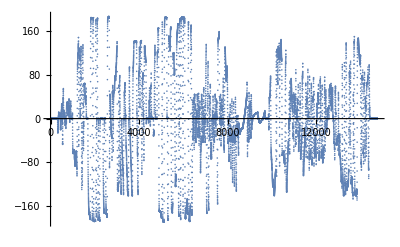

```mathematica
ListPlot[vl]
```

```mathematica
ListPointPlot3D[Transpose[{vl, vf, ω}], PlotRange->All]
```